```mathematica
(* Ejemplo 1*)
```

WolframAlphaQueryParseResults

2.718281828459045235360287471352662497757247093699959574966967627724076630353547594571382178525166427

WolframAlphaQueryParseResults

1. ⅈ

```mathematica
(* Ejemplo 2*)
```

WolframAlphaQueryResults

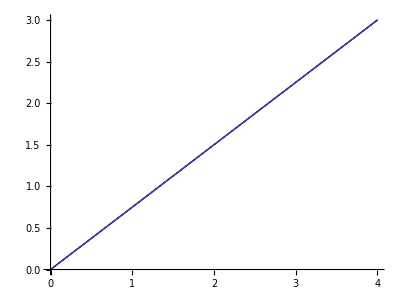

WolframAlphaQueryResults

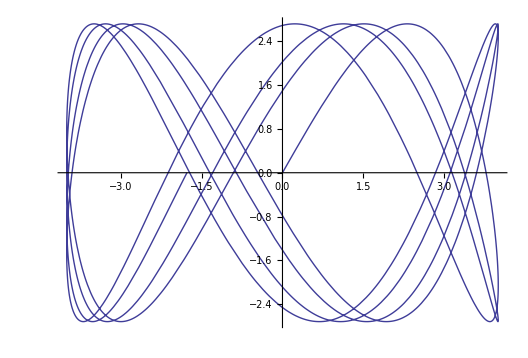

WolframAlphaQueryResults

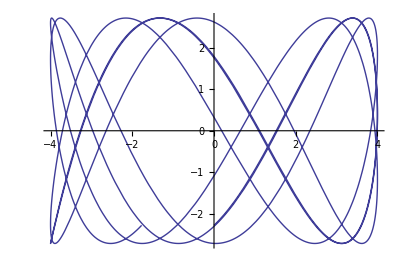

```mathematica
(* Ejemplo 3*)
```

WolframAlphaQueryResults

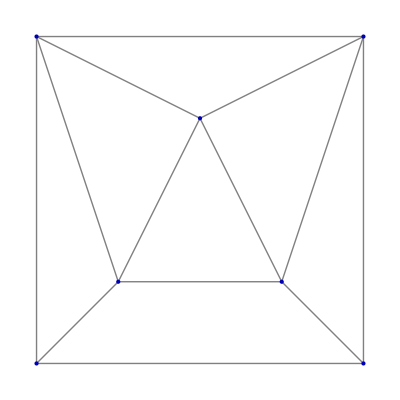
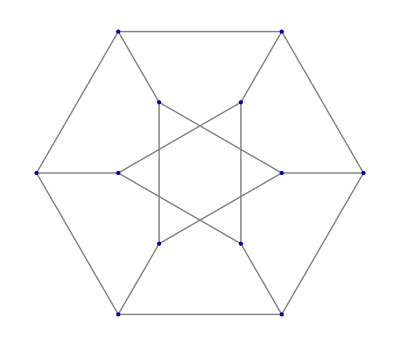
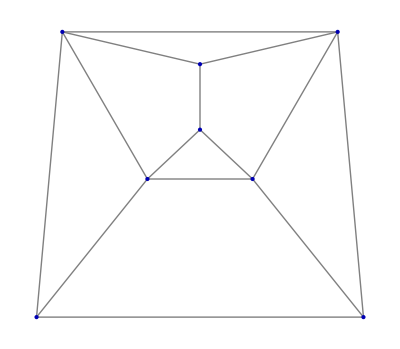
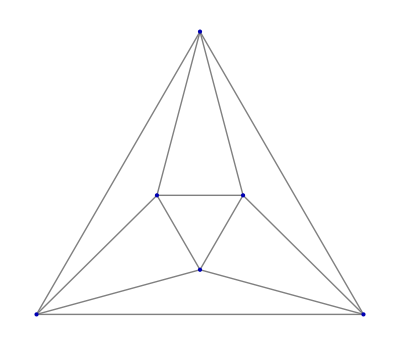
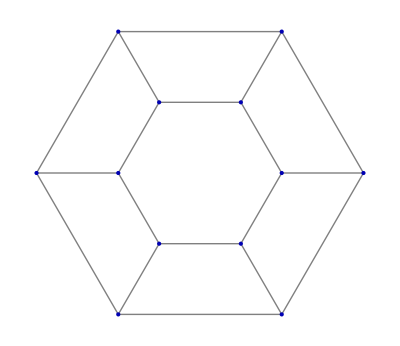
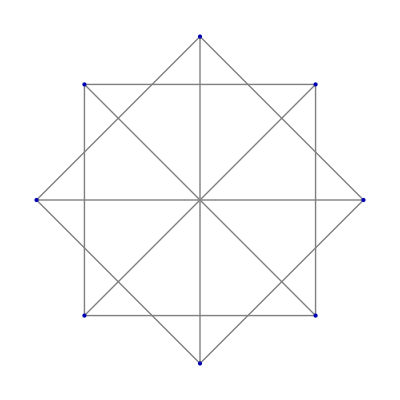
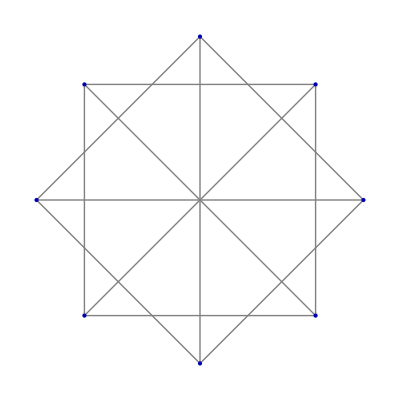
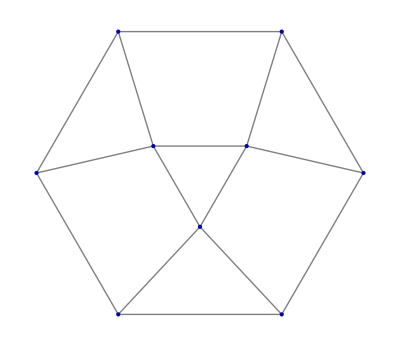
| skeleton graph name
augmented triangular prism | Johnson solid skeleton 49
Dürer's solid | Dürer graph
gyrobifastigium | Johnson solid skeleton 26
regular octahedron | octahedral graph
unit equilateral hexagonal prism | 6-prism graph
stella octangula | 8-circulant graph (2,4)
tetrahedron 2-compound | 8-circulant graph (2,4)
triangular cupola | Johnson solid skeleton 3
tridiminished icosahedron | Johnson solid skeleton 63
truncated tetrahedron | truncated tetrahedral graph
 | skeleton image
augmented triangular prism | -Graphics-
Dürer's solid | -Graphics-
gyrobifastigium | -Graphics-
regular octahedron | -Graphics-
unit equilateral hexagonal prism | -Graphics-
stella octangula | -Graphics-
tetrahedron 2-compound | -Graphics-
triangular cupola | -Graphics-
tridiminished icosahedron | -Graphics-
truncated tetrahedron | -Graphics-

```mathematica
(* Ejemplo 4*)
```

WolframAlphaQueryParseResults

1/2 √π Erf[x]

WolframAlphaQueryParseResults

```mathematica
Gamma[π]
(* Ejemplo 5*)
```

```mathematica
{{ClearAll[star];
estrella=
{{AbsoluteThickness[2],Line[{{0,1},{Cos[210 Degree],Sin[210 Degree]},{Cos[330 Degree],Sin[330 Degree]},{0,1}}]},
{AbsoluteThickness[2],Line[{{Cos[30 Degree],Sin[30 Degree]},{Cos[150 Degree],Sin[150 Degree]},{Cos[270 Degree],Sin[270 Degree]},{Cos[30 Degree],Sin[30 Degree]}}]}};
star[1]=estrella;
star[n_]:=star[n]=Rotate[Scale[star[n-1],0.5773],30 Degree];
nova[n_]:=Graphics[{star[n]}]
constelacion0=Table[nova[i],{i,1,23}];
constelacion=Append[constelacion0,{}];
Show[constelacion0]}, {□}}
```

{{Null^7 -Graphics-},{□}}

```mathematica
(* Tube problemas con las entradas porque apareciían null y varios codigos se perdieron*)
```

```mathematica
15^2015
```

WolframAlphaQueryResults

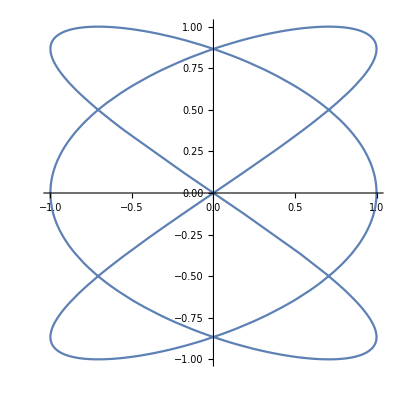

WolframAlphaQueryResults

WolframAlpha::timeout: The call to WolframAlpha["ParametricPlot [ {Sin(3t),Sin(2t+pi/4)} ,{t,0,2*pi}]", "MathematicaParse"] has exceeded 30. seconds. Increasing the value of the TimeConstraint option may improve the result.

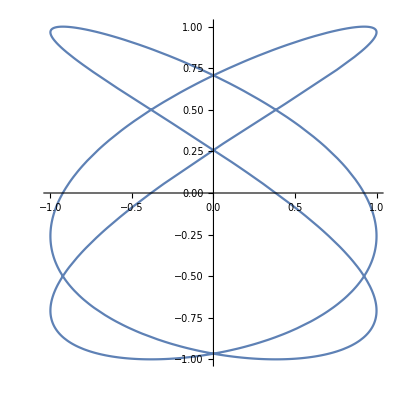

WolframAlphaQueryResults

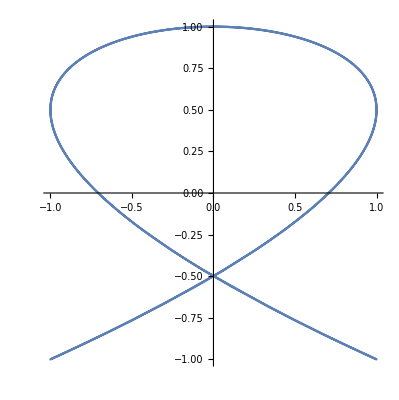

WolframAlphaQueryResults

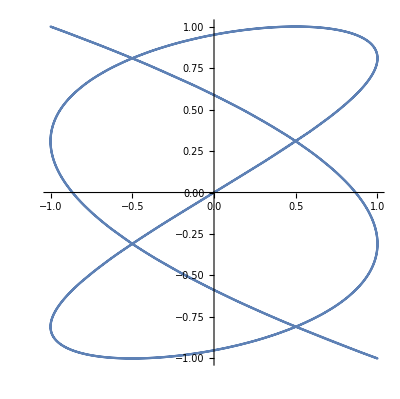

WolframAlphaQueryResults

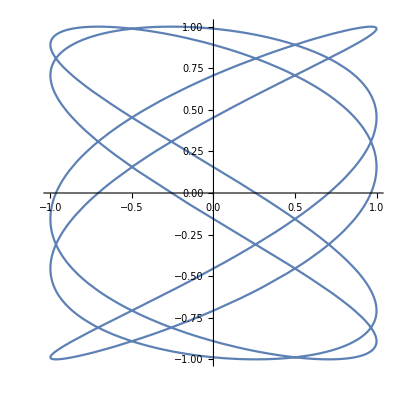

WolframAlphaQueryResults

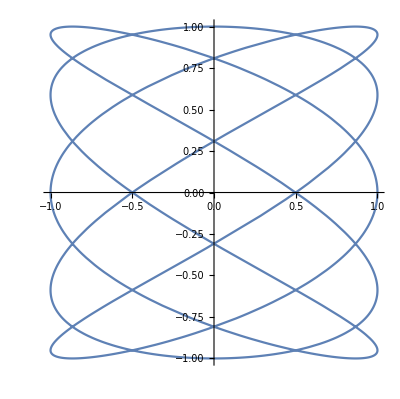
```mathematica
-Graphics-
(* Ejemplo 6*)
```

```mathematica
map=Join@@((List@@First@CountryData[#,"Polygon"])&/@CountryData[]);
```

```mathematica
coordsToXYZ[list_]:=Transpose[{Cos[#[[1]]]*Cos[#[[2]]],Cos[#[[1]]]*Sin[#[[2]]],Sin[#[[1]]]}&@Reverse@Transpose[list*Pi/180.]];
```

```mathematica
stations=WeatherData[];
```

```mathematica
coords=coordsToXYZ[{WeatherData[#,"Longitude"],WeatherData[#,"Latitude"]}&/@stations];
```

```mathematica
globe=First@ParametricPlot3D[.99*{Sin[u] Sin[v],Cos[u]Sin[v],Cos[v]},{u,-π,π},{v,-π, π},MaxRecursion->4,Axes->None,PlotStyle->Opacity[.5]];
```

```mathematica
Graphics3D[{globe,Black,Line/@coordsToXYZ/@map ,Red,Point@coords},Boxed->False,ImageSize->Medium,Lighting->"Neutral"]
```

-Graphics3D-

```mathematica
(* Ejemplo 7*)
```

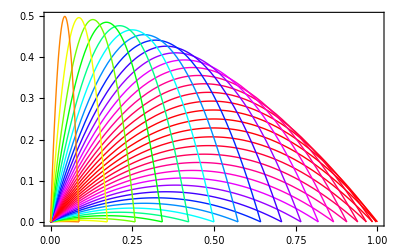

```mathematica
graficas=Table[β=θ/180*π;col=Sin[2β];Plot[Tan[β]x-1/2*x^2/Cos[β]^2,{x,0,Sin[2*β]},PlotStyle->{Hue[col]}],{θ,2.5,87.5,2.5}];
Show[graficas,PlotRange->{Automatic,Automatic},Frame->True]
```

```mathematica
(* Ejemplo 8*)
```

```mathematica
object=Import["ExampleData/helicopter.dxf.gz", ImageSize -> Medium]
Show[object/.Polygon[{a_,b_,c_}]->Polygon[{a,b/2,2 c}],ImageSize->400,ViewAngle->.2]
```

-Graphics3D-

-Graphics3D-

```mathematica
(* Ejemplo 9*)
```

```mathematica
N [E,100];
pi=N[E,10000];
Partition[RealDigits[pi][[1]],100];
Histogram[Total[#]&/@Partition[RealDigits[pi][[1]],10]]
```

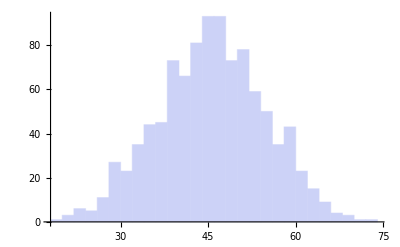

```mathematica
(* Ejemplo 10*)
```

```mathematica
Import["C:\Users\ma.rojas11\Downloads\Free_chair_set_04.dxf",ImageSize -> Medium]
```

-Graphics3D-